# Gradient Force Sanity Checking

## Initialization

```mathematica
Q;
```

```mathematica
Q:=Quit[]
```

```mathematica
Off[General::obspkg]
<<VectorAnalysis`
```

```mathematica
Off[Solve::inex]
```

```mathematica
SetOptions[$FrontEndSession,"DefaultPrecision"->MachinePrecision,"DefaultRealPrecision"->MachinePrecision]
```

```mathematica
SetCoordinates[Cartesian[x,y,z]]
```

Cartesian[x,y,z]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bretton/Documents/School/Research/Optical-Binding-Simulation

```mathematica
$Assumptions={kg>0,second>0,meter>0,kelvin>0,coulomb>0,ϵb>0};
```

```mathematica
xx={1,0,0};
yy={0,1,0};
zz={0,0,1};
```

## Definitions

### Fundamental

```mathematica
ϵ0=8.85 10^-12 farad/meter
μ0=4π 10^-7 henry/meter
η0=√(μ0/ϵ0);
c=1/(√(ϵ0 μ0))//Simplify
kB=1.38 10^-23(kg meter^2)/(second^2 kelvin)
```

(8.85×10^-12 farad)/meter

(henry π)/(2500000 meter)

(2.99863×10^8 meter)/(√(farad henry))

(1.38×10^-23 kg meter^2)/(kelvin second^2)

### Colloid properties

```mathematica
a=500. 10^-9 meter
VOL=4/3 π a^3
ρSiO2=2320 kg/meter^3
mass=VOL ρSiO2
μ=1.6 10^-3 kg/(meter second) (*Dynamic Viscosity*)
γ=(6π μ a)/mass(*drag frequency*)
```

5.×10^-7 meter

5.23599×10^-19 meter^3

(2320 kg)/meter^3

1.21475×10^-15 kg

(0.0016 kg)/(meter second)

(1.24138×10^7)/second

```mathematica
T=300kelvin
```

300 kelvin

## Units

```mathematica
henry=henry/.Flatten[Solve[(farad henry)/meter^2==second^2/meter^2,henry]]
```

second^2/farad

```mathematica
(*kg=kg/.Flatten[Solve[newton==kg meter second^-2,kg]]*)
```

```mathematica
farad=coulomb/volt
volt=joule/coulomb
ampere=coulomb/second
joule=kg meter^2 second^-2
watt=joule/second
(*nm=meter 10^-9;
μm=meter 10^-6;*)
```

coulomb/volt

joule/coulomb

coulomb/second

(kg meter^2)/second^2

(kg meter^2)/second^3

```mathematica
second=10^6 microsecond
kg=10^9 microgram
meter=10^9 nanometer
coulomb=10^15 femtocoulomb
```

1000000 microsecond

1000000000 microgram

1000000000 nanometer

1000000000000000 femtocoulomb

```mathematica
microsecond=1
microgram=1
nanometer=1
femtocoulomb=1
```

1

1

1

«1 more identical outputs»

## Laser

```mathematica
λ=600.  10^-9 meter
area=100.(10^-6 meter)^2 
power=1000 watt
```

600.

1.×10^8

1000000000000

```mathematica
I0=power/area
```

10000.

```mathematica
I0
```

10000.

## Polarizability

```mathematica
ϵp=-3(1.33)^2(*SiO2*)
μp=1
ϵb=1.33^2(*SiO2*)
μb=1
ηb=√(μb/ϵb)
k0=(2π)/λ
ω=k0 c
k=k0 √ϵb
αsr=4π ϵ0 ϵb a^3(ϵp-ϵb)/(ϵp+2 ϵb)
αs=(1/αsr-ⅈ k^3/(6 π ϵ0 ϵb))^-1
```

-5.3067

1

1.7689

1

0.75188

0.010472

3.14016×10^9

0.0139277

98361.8

0.121279+109.221 ⅈ

```mathematica
k^3/(6 π ϵ0 ϵb)
```

0.00915573

```mathematica
1/αsr
```

0.0000101665

```mathematica
αr=ComplexExpand[Re[αsr]]//Simplify
αi=ComplexExpand[Im[αsr]]//Simplify
```

98361.8

0

## Physical Setup

```mathematica
L=25 10^-6 meter (*computational area*)
```

25000

```mathematica
NN=3 (*Number of Particles*)
```

3

```mathematica
α=αr+ⅈ αi
```

98361.8

```mathematica
SeedRandom[1001010]
```

RandomGeneratorState[…]

```mathematica
polarizabilities=Table[{αx[m]=α,αy[m]=α,αz[m]=α},{m,1,NN}]
```

{{98361.8,98361.8,98361.8},{98361.8,98361.8,98361.8},{98361.8,98361.8,98361.8}}

```mathematica
positions[0]=Table[{X[0][m]=RandomReal[{-L/2,L/2}],Y[0][m]=RandomReal[{-L/2,L/2}],Z[0][m]=RandomReal[{-L/2,L/2}]},{m,1,NN}]
```

{{-9888.3,-1688.19,10996.},{-11854.3,-4905.48,-2754.85},{1644.37,6523.84,2778.41}}

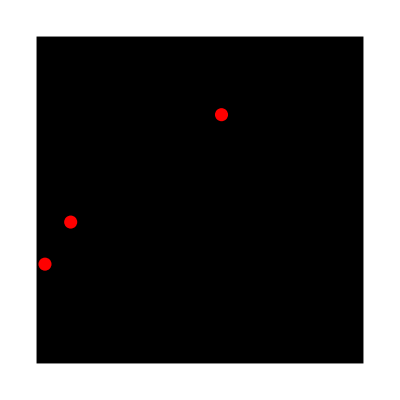

```mathematica
FRAME[0]=Graphics[{Rectangle[{-(L/2),-(L/2)},{L/2,L/2}],{Red,Table[Disk[{X[0][m],Y[0][m]},a],{m,1,NN}]}}]
```

## Green' s Function

```mathematica
k
```

0.0139277

```mathematica
ϵ0
```

8.85×10^-6

```mathematica
ϵb
```

1.7689

```mathematica
G[x_,y_,z_]={{(ⅇ^(ⅈ k √(x^2+y^2+z^2)) ((y^2+z^2) (-1+k^2 (y^2+z^2)+ⅈ k √(x^2+y^2+z^2))+x^2 (2+k^2 (y^2+z^2)-2 ⅈ k √(x^2+y^2+z^2))))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x y (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)},{-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x y (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)ⅇ^(ⅈ k √(x^2+y^2+z^2)) (k^2 x^4+z^2 (-1+k^2 z^2+ⅈ k √(x^2+y^2+z^2))+y^2 (2+k^2 z^2-2 ⅈ k √(x^2+y^2+z^2))+x^2 (-1+ⅈ k √(x^2+y^2+z^2)+k^2 (y^2+2 z^2))),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) y z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)},{-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) y z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)ⅇ^(ⅈ k √(x^2+y^2+z^2)) (k^2 x^4+k^2 y^4+2 z^2 (1-ⅈ k √(x^2+y^2+z^2))+y^2 (-1+k^2 z^2+ⅈ k √(x^2+y^2+z^2))+x^2 (-1+ⅈ k √(x^2+y^2+z^2)+k^2 (2 y^2+z^2)))}}//Simplify;
```

```mathematica
GG[step_][n_][m_]=G[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GG[step_][n_][n_]=-{{1/αx[n],0,0},{0,1/αy[n],0},{0,0,1/αz[n]}};
```

```mathematica
GG[0][n_][m_]=G[X[0][n]-X[0][m],Y[0][n]-Y[0][m],Z[0][n]-Z[0][m]];
GG[0][n_][n_]=-{{1/αx[n],0,0},{0,1/αy[n],0},{0,0,1/αz[n]}};
```

```mathematica
GG[0][2][1]//TraditionalForm
```

(-0.0000531111-0.0000422091 ⅈ | 1.67068×10^-6+1.35596×10^-6 ⅈ | 7.14055×10^-6+5.79542×10^-6 ⅈ
1.67068×10^-6+1.35596×10^-6 ⅈ | -0.0000513979-0.0000408187 ⅈ | 0.0000116853+9.48406×10^-6 ⅈ
7.14055×10^-6+5.79542×10^-6 ⅈ | 0.0000116853+9.48406×10^-6 ⅈ | -4.18838×10^-6-2.50239×10^-6 ⅈ)

```mathematica
GGtest = Table[GG[0][n][m], {n, 1, NN}, {m, 1, NN}];
```

## Incident Field

```mathematica
w0=L/4
Einc[x_,y_,z_]=E0 xx Exp[ⅈ k z]Exp[-(x^2+y^2)/w0^2]
```

6250

{ⅇ^((-x^2-y^2)/39062500+(0.+0.0139277 ⅈ) z) E0,0,0}

```mathematica
EEi[step_][n_]=Einc[X[step][n],Y[step][n],Z[step][n]]
EEi[0][n_]=Einc[X[0][n],Y[0][n],Z[0][n]]
```

{ⅇ^((-(X[step][n])^2-(Y[step][n])^2)/39062500+(0.+0.0139277 ⅈ) Z[step][n]) E0,0,0}

{ⅇ^((-(X[0][n])^2-(Y[0][n])^2)/39062500+(0.+0.0139277 ⅈ) Z[0][n]) E0,0,0}

```mathematica
E0=√(2η0 ηb I0)
```

0.0752759

```mathematica
EEiTest = Table[EEi[0][n],{n,1,NN}];
```

## Unknown Variables

```mathematica
pp[step_][m_]={px[step][m],py[step][m],pz[step][m]}
```

{px[step][m],py[step][m],pz[step][m]}

```mathematica
pp[0][m_]={px[0][m],py[0][m],pz[0][m]}
```

{px[0][m],py[0][m],pz[0][m]}

## Equations

```mathematica
eqX[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).xx
eqY[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).yy
eqZ[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).zz
```

```mathematica
eqs[step_]=Flatten[Table[{eqX[step][m]==0,eqY[step][m]==0,eqZ[step][m]==0},{m,1,NN}]]
```

```mathematica
unk[step_]=Flatten[Table[{px[step][m],py[step][m],pz[step][m]},{m,1,NN}]]
```

{px[step][1],py[step][1],pz[step][1],px[step][2],py[step][2],pz[step][2],px[step][3],py[step][3],pz[step][3]}

```mathematica
sol[0]=Solve[eqs[0],unk[0]]//Flatten
```

{px[0][1]→-122.948+82.3661 ⅈ,py[0][1]→-29.6575-3.44461 ⅈ,pz[0][1]→-237.718+306.493 ⅈ,px[0][2]→-24.3756+65.8578 ⅈ,py[0][2]→219.569+131.375 ⅈ,pz[0][2]→442.48+222.299 ⅈ,px[0][3]→-162.147+81.2746 ⅈ,py[0][3]→69.8821-72.5192 ⅈ,pz[0][3]→88.9062+21.2349 ⅈ}

```mathematica
Evaluate[unk[0]]=(unk[0]/.sol[0])
```

{-122.948+82.3661 ⅈ,-29.6575-3.44461 ⅈ,-237.718+306.493 ⅈ,-24.3756+65.8578 ⅈ,219.569+131.375 ⅈ,442.48+222.299 ⅈ,-162.147+81.2746 ⅈ,69.8821-72.5192 ⅈ,88.9062+21.2349 ⅈ}

## Total Field

```mathematica
EEtot[step_][x_,y_,z_]=Einc[x,y,z]+Sum[G[x-X[step][m],y-Y[step][m],z-Z[step][m]].pp[step][m],{m,1,NN}];
```

```mathematica
II[step_][x_,y_,z_]=EEtot[step][x,y,z].(EEtot[step][x,y,z]/.ⅈ->-ⅈ);
```

```mathematica
(*DensityPlot[II[x,y,0],{x, -15λ,15λ},{y, -15λ,15λ},PlotPoints->50]*)
```

## Scattering at site m from all other particles

```mathematica
ESC[step_][m_][x_,y_,z_]:=Sum[G[x-X[step][i],y-Y[step][i],z-Z[step][i]].pp[step][i],{i,Drop[Table[j,{j,1,NN}],{m}]}]
```

```mathematica
ESCmi = Table[ESC[0][m][X[0][m],Y[0][m],Z[0][m]], {m, 1, NN}];
```

```mathematica
Etot[step_][m_][x_,y_,z_]:=Einc[x,y,z]+ESC[step][m][x,y,z]
```

```mathematica
Htot[step_][m_][x_,y_,z_]:=Curl[Etot[step][m][x,y,z]]/(ⅈ ω μ0 μb)
```

## Force on particle m

### Complex Force (must take real part)

```mathematica
cplxFF[step_][m_]:=((αr/4)Grad[Etot[step][m][x,y,z].(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]+αi (k/(ϵ0 ϵb))(1/2)(Cross[Etot[step][m][x,y,z],(Htot[step][m][x,y,z]/.ⅈ->-ⅈ)]/c)+αi (k/(ϵ0 ϵb))c Curl[(ϵ0 ϵb/(4 ω ⅈ))Cross[Etot[step][m][x,y,z],(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
```

```mathematica
cplxGradFF[step_][m_]:=((αr/4)Grad[Etot[step][m][x,y,z].(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
cplxRadPFF[step_][m_]:=(αi (k/(ϵ0 ϵb))(1/2)(Cross[Etot[step][m][x,y,z],(Htot[step][m][x,y,z]/.ⅈ->-ⅈ)]/c))/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
cplxSpinFF[step_][m_]:=(αi (k/(ϵ0 ϵb))c Curl[(ϵ0 ϵb/(4 ω ⅈ))Cross[Etot[step][m][x,y,z],(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
```

### Force on all particles

```mathematica
Table[GradFF[0][m]=Re[cplxGradFF[0][m]],{m,1,NN}]
```

{{-0.00348016,-0.00237851,0.00921858},{0.0130679,0.0110593,0.00408889},{-0.00938413,-0.0080544,0.00713527}}

```mathematica
Table[RadPFF[0][m]=Re[cplxRadPFF[0][m]],{m,1,NN}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
Table[SpinFF[0][m]=Re[cplxSpinFF[0][m]],{m,1,NN}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
forces[0]=Table[FF[0][m]={Re[cplxFF[0][m]][[1]],Re[cplxFF[0][m]][[2]],0Re[cplxFF[0][m]][[3]]},{m,1,NN}]
```

{{-0.00348016,-0.00237851,0.},{0.0130679,0.0110593,0.},{-0.00938413,-0.0080544,0.}}